```mathematica
Rho1s=300;
C1s=1377;
k1s=0.082;
Rho2s=862;
C2s=2100;
k2s=0.37;
Rho3s=74.2;
C3s=1726;
k3s=0.045;
Rho4s=1.18;
C4s=1005;
k4s=0.028;
ks1=25;
ks2=9;
a1s=k1s/(C1s*Rho1s);
a2s=k2s/(C2s*Rho2s);
a3s=k3s/(C3s*Rho3s);
a4s=k4s/(C4s*Rho4s);
x1s=0.0006;x2s=0.006;x3s=0.0036;x4s=0.005;ts=1700;
```

```mathematica
Sol=Table[0,{i,1,110},{j,1,170001}];
For[cnt=1,cnt≤170001,cnt++,Sol[[1]][[cnt]]=75;Sol[[110]][[cnt]]=37
]
For[cnt=2,cnt≤110,cnt++,Sol[[cnt]][[1]]=37
]
```

```mathematica
dy=0.01;dx1=0.0001;dx2=0.0001;dx3=0.0001;dx4=0.001;
sigma1=a1s*dy/(dx1*dx1);sigma2=a2s*dy/(dx2*dx2);sigma3=a3s*dy/(dx3*dx3);sigma4=a4s*dy/(dx4*dx4);
```

```mathematica
For[j=2,j≤170001,j++,
{
For[i=3,i≤7,i++,
Sol[[i]][[j]]=sigma1*Sol[[i+1]][[j-1]]+sigma1*Sol[[i-1]][[j-1]]-(2*sigma1-1)*Sol[[i]][[j-1]]
];
For[i=9,i≤67,i++,
Sol[[i]][[j]]=sigma2*Sol[[i+1]][[j-1]]+sigma2*Sol[[i-1]][[j-1]]-(2*sigma2-1)*Sol[[i]][[j-1]]
];
For[i=69,i≤103,i++,
Sol[[i]][[j]]=sigma3*Sol[[i+1]][[j-1]]+sigma3*Sol[[i-1]][[j-1]]-(2*sigma3-1)*Sol[[i]][[j-1]]
];
For[i=105,i≤108,i++,
Sol[[i]][[j]]=sigma4*Sol[[i+1]][[j-1]]+sigma4*Sol[[i-1]][[j-1]]-(2*sigma4-1)*Sol[[i]][[j-1]]
];
Sol[[2]][[j]]=(Sol[[3]][[j]]-Sol[[1]][[j]])/(k1s/dx1+ks1)*k1s/dx1+Sol[[1]][[j]];
Sol[[8]][[j]]=(Sol[[9]][[j]]-Sol[[7]][[j]])/(k1s/dx1+k2s/dx2)*k2s/dx2+Sol[[7]][[j]];
Sol[[68]][[j]]=(Sol[[69]][[j]]-Sol[[67]][[j]])/(k2s/dx2+k3s/dx3)*k3s/dx3+Sol[[67]][[j]];
Sol[[104]][[j]]=(Sol[[105]][[j]]-Sol[[103]][[j]])/(k3s/dx3+ks2)*ks2+Sol[[103]][[j]];
Sol[[109]][[j]]=(Sol[[110]][[j]]-Sol[[108]][[j]])/(k4s/dx4+ks2)*ks2+Sol[[108]][[j]]
}
]
```

```mathematica
mesh=Table[Sol[[i]][[100*j+1]],{i,1,110},{j,0,1700}];
```

```mathematica
mesh[[109]]
```

{37,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.0001,37.0001,37.0003,37.0005,37.0008,37.0013,37.002,37.0029,37.004,37.0055,37.0072,37.0093,37.0118,37.0147,37.018,37.0217,37.0258,37.0304,37.0355,37.0411,37.0471,37.0536,37.0605,37.068,37.0759,37.0842,37.093,37.1023,37.112,37.1221,37.1327,37.1437,37.155,37.1668,37.1789,37.1914,37.2042,37.2174,37.2309,37.2447,37.2588,37.2733,37.288,37.303,37.3182,37.3337,37.3494,37.3654,37.3815,37.3979,37.4145,37.4313,37.4482,37.4653,37.4826,37.5,37.5176,37.5354,37.5532,37.5712,37.5893,37.6075,37.6259,37.6443,37.6628,37.6814,37.7001,37.7188,37.7377,37.7566,37.7756,37.7946,37.8137,37.8328,37.852,37.8712,37.8904,37.9097,37.9291,37.9484,37.9678,37.9872,38.0066,38.0261,38.0455,38.065,38.0845,38.104,38.1235,38.143,38.1625,38.182,38.2016,38.2211,38.2406,38.2601,38.2796,38.2991,38.3185,38.338,38.3575,38.3769,38.3964,38.4158,38.4352,38.4546,38.4739,38.4933,38.5126,38.5319,38.5512,38.5705,38.5898,38.609,38.6282,38.6474,38.6666,38.6857,38.7048,38.7239,38.743,38.762,38.781,38.8,38.819,38.8379,38.8568,38.8757,38.8946,38.9134,38.9322,38.951,38.9697,38.9884,39.0071,39.0258,39.0444,39.063,39.0816,39.1001,39.1186,39.1371,39.1556,39.174,39.1924,39.2107,39.2291,39.2474,39.2656,39.2839,39.3021,39.3203,39.3384,39.3565,39.3746,39.3927,39.4107,39.4287,39.4467,39.4646,39.4825,39.5004,39.5182,39.536,39.5538,39.5716,39.5893,39.607,39.6246,39.6422,39.6598,39.6774,39.695,39.7125,39.7299,39.7474,39.7648,39.7822,39.7995,39.8169,39.8342,39.8514,39.8687,39.8859,39.903,39.9202,39.9373,39.9544,39.9714,39.9885,40.0054,40.0224,40.0393,40.0562,40.0731,40.09,40.1068,40.1236,40.1403,40.157,40.1737,40.1904,40.207,40.2237,40.2402,40.2568,40.2733,40.2898,40.3063,40.3227,40.3391,40.3555,40.3718,40.3881,40.4044,40.4207,40.4369,40.4531,40.4693,40.4854,40.5016,40.5176,40.5337,40.5497,40.5657,40.5817,40.5977,40.6136,40.6295,40.6453,40.6612,40.677,40.6927,40.7085,40.7242,40.7399,40.7556,40.7712,40.7868,40.8024,40.8179,40.8335,40.849,40.8644,40.8799,40.8953,40.9107,40.9261,40.9414,40.9567,40.972,40.9872,41.0025,41.0177,41.0328,41.048,41.0631,41.0782,41.0933,41.1083,41.1233,41.1383,41.1533,41.1682,41.1831,41.198,41.2128,41.2277,41.2425,41.2572,41.272,41.2867,41.3014,41.3161,41.3307,41.3453,41.3599,41.3745,41.389,41.4036,41.418,41.4325,41.4469,41.4614,41.4757,41.4901,41.5044,41.5188,41.533,41.5473,41.5615,41.5757,41.5899,41.6041,41.6182,41.6323,41.6464,41.6605,41.6745,41.6885,41.7025,41.7164,41.7304,41.7443,41.7582,41.772,41.7859,41.7997,41.8135,41.8272,41.841,41.8547,41.8684,41.882,41.8957,41.9093,41.9229,41.9365,41.95,41.9635,41.977,41.9905,42.0039,42.0174,42.0308,42.0441,42.0575,42.0708,42.0841,42.0974,42.1107,42.1239,42.1371,42.1503,42.1635,42.1766,42.1897,42.2028,42.2159,42.2289,42.242,42.255,42.2679,42.2809,42.2938,42.3067,42.3196,42.3325,42.3453,42.3582,42.371,42.3837,42.3965,42.4092,42.4219,42.4346,42.4473,42.4599,42.4725,42.4851,42.4977,42.5102,42.5227,42.5352,42.5477,42.5602,42.5726,42.585,42.5974,42.6098,42.6222,42.6345,42.6468,42.6591,42.6713,42.6836,42.6958,42.708,42.7202,42.7323,42.7445,42.7566,42.7687,42.7807,42.7928,42.8048,42.8168,42.8288,42.8407,42.8527,42.8646,42.8765,42.8884,42.9002,42.9121,42.9239,42.9357,42.9474,42.9592,42.9709,42.9826,42.9943,43.006,43.0176,43.0293,43.0409,43.0525,43.064,43.0756,43.0871,43.0986,43.1101,43.1215,43.133,43.1444,43.1558,43.1672,43.1785,43.1899,43.2012,43.2125,43.2238,43.2351,43.2463,43.2575,43.2687,43.2799,43.2911,43.3022,43.3133,43.3244,43.3355,43.3466,43.3576,43.3686,43.3796,43.3906,43.4016,43.4125,43.4235,43.4344,43.4453,43.4561,43.467,43.4778,43.4886,43.4994,43.5102,43.5209,43.5317,43.5424,43.5531,43.5637,43.5744,43.585,43.5957,43.6063,43.6168,43.6274,43.638,43.6485,43.659,43.6695,43.6799,43.6904,43.7008,43.7112,43.7216,43.732,43.7424,43.7527,43.763,43.7733,43.7836,43.7939,43.8042,43.8144,43.8246,43.8348,43.845,43.8551,43.8653,43.8754,43.8855,43.8956,43.9057,43.9157,43.9257,43.9358,43.9458,43.9557,43.9657,43.9756,43.9856,43.9955,44.0054,44.0152,44.0251,44.0349,44.0448,44.0546,44.0644,44.0741,44.0839,44.0936,44.1033,44.113,44.1227,44.1324,44.142,44.1517,44.1613,44.1709,44.1805,44.19,44.1996,44.2091,44.2186,44.2281,44.2376,44.247,44.2565,44.2659,44.2753,44.2847,44.2941,44.3035,44.3128,44.3221,44.3315,44.3408,44.35,44.3593,44.3685,44.3778,44.387,44.3962,44.4054,44.4145,44.4237,44.4328,44.4419,44.451,44.4601,44.4692,44.4782,44.4873,44.4963,44.5053,44.5143,44.5233,44.5322,44.5412,44.5501,44.559,44.5679,44.5768,44.5856,44.5945,44.6033,44.6121,44.6209,44.6297,44.6385,44.6472,44.6559,44.6647,44.6734,44.6821,44.6907,44.6994,44.708,44.7167,44.7253,44.7339,44.7425,44.751,44.7596,44.7681,44.7766,44.7851,44.7936,44.8021,44.8106,44.819,44.8275,44.8359,44.8443,44.8527,44.861,44.8694,44.8777,44.8861,44.8944,44.9027,44.9109,44.9192,44.9275,44.9357,44.9439,44.9521,44.9603,44.9685,44.9767,44.9848,44.993,45.0011,45.0092,45.0173,45.0254,45.0334,45.0415,45.0495,45.0576,45.0656,45.0736,45.0815,45.0895,45.0975,45.1054,45.1133,45.1212,45.1291,45.137,45.1449,45.1527,45.1606,45.1684,45.1762,45.184,45.1918,45.1996,45.2073,45.2151,45.2228,45.2305,45.2382,45.2459,45.2536,45.2612,45.2689,45.2765,45.2841,45.2917,45.2993,45.3069,45.3145,45.322,45.3296,45.3371,45.3446,45.3521,45.3596,45.3671,45.3745,45.382,45.3894,45.3968,45.4042,45.4116,45.419,45.4264,45.4337,45.4411,45.4484,45.4557,45.463,45.4703,45.4776,45.4848,45.4921,45.4993,45.5066,45.5138,45.521,45.5281,45.5353,45.5425,45.5496,45.5568,45.5639,45.571,45.5781,45.5852,45.5923,45.5993,45.6064,45.6134,45.6204,45.6274,45.6344,45.6414,45.6484,45.6553,45.6623,45.6692,45.6762,45.6831,45.69,45.6969,45.7037,45.7106,45.7174,45.7243,45.7311,45.7379,45.7447,45.7515,45.7583,45.7651,45.7718,45.7785,45.7853,45.792,45.7987,45.8054,45.8121,45.8187,45.8254,45.8321,45.8387,45.8453,45.8519,45.8585,45.8651,45.8717,45.8782,45.8848,45.8913,45.8979,45.9044,45.9109,45.9174,45.9239,45.9303,45.9368,45.9433,45.9497,45.9561,45.9625,45.9689,45.9753,45.9817,45.9881,45.9944,46.0008,46.0071,46.0134,46.0198,46.0261,46.0324,46.0386,46.0449,46.0512,46.0574,46.0636,46.0699,46.0761,46.0823,46.0885,46.0946,46.1008,46.107,46.1131,46.1193,46.1254,46.1315,46.1376,46.1437,46.1498,46.1558,46.1619,46.168,46.174,46.18,46.186,46.1921,46.198,46.204,46.21,46.216,46.2219,46.2279,46.2338,46.2397,46.2456,46.2515,46.2574,46.2633,46.2692,46.275,46.2809,46.2867,46.2926,46.2984,46.3042,46.31,46.3158,46.3215,46.3273,46.3331,46.3388,46.3445,46.3503,46.356,46.3617,46.3674,46.3731,46.3787,46.3844,46.3901,46.3957,46.4014,46.407,46.4126,46.4182,46.4238,46.4294,46.435,46.4405,46.4461,46.4516,46.4572,46.4627,46.4682,46.4737,46.4792,46.4847,46.4902,46.4956,46.5011,46.5065,46.512,46.5174,46.5228,46.5282,46.5336,46.539,46.5444,46.5498,46.5551,46.5605,46.5658,46.5712,46.5765,46.5818,46.5871,46.5924,46.5977,46.603,46.6082,46.6135,46.6187,46.624,46.6292,46.6344,46.6396,46.6448,46.65,46.6552,46.6604,46.6656,46.6707,46.6759,46.681,46.6861,46.6913,46.6964,46.7015,46.7066,46.7116,46.7167,46.7218,46.7268,46.7319,46.7369,46.742,46.747,46.752,46.757,46.762,46.767,46.772,46.7769,46.7819,46.7868,46.7918,46.7967,46.8016,46.8065,46.8114,46.8163,46.8212,46.8261,46.831,46.8359,46.8407,46.8456,46.8504,46.8552,46.86,46.8648,46.8697,46.8744,46.8792,46.884,46.8888,46.8935,46.8983,46.903,46.9078,46.9125,46.9172,46.9219,46.9266,46.9313,46.936,46.9407,46.9454,46.95,46.9547,46.9593,46.9639,46.9686,46.9732,46.9778,46.9824,46.987,46.9916,46.9962,47.0007,47.0053,47.0098,47.0144,47.0189,47.0235,47.028,47.0325,47.037,47.0415,47.046,47.0505,47.0549,47.0594,47.0639,47.0683,47.0728,47.0772,47.0816,47.086,47.0905,47.0949,47.0993,47.1036,47.108,47.1124,47.1168,47.1211,47.1255,47.1298,47.1341,47.1385,47.1428,47.1471,47.1514,47.1557,47.16,47.1642,47.1685,47.1728,47.177,47.1813,47.1855,47.1898,47.194,47.1982,47.2024,47.2066,47.2108,47.215,47.2192,47.2234,47.2275,47.2317,47.2359,47.24,47.2441,47.2483,47.2524,47.2565,47.2606,47.2647,47.2688,47.2729,47.277,47.281,47.2851,47.2892,47.2932,47.2973,47.3013,47.3053,47.3093,47.3134,47.3174,47.3214,47.3254,47.3294,47.3333,47.3373,47.3413,47.3452,47.3492,47.3531,47.3571,47.361,47.3649,47.3688,47.3727,47.3766,47.3805,47.3844,47.3883,47.3922,47.396,47.3999,47.4038,47.4076,47.4114,47.4153,47.4191,47.4229,47.4267,47.4305,47.4343,47.4381,47.4419,47.4457,47.4495,47.4532,47.457,47.4608,47.4645,47.4682,47.472,47.4757,47.4794,47.4831,47.4868,47.4905,47.4942,47.4979,47.5016,47.5053,47.5089,47.5126,47.5163,47.5199,47.5235,47.5272,47.5308,47.5344,47.538,47.5417,47.5453,47.5489,47.5524,47.556,47.5596,47.5632,47.5667,47.5703,47.5739,47.5774,47.5809,47.5845,47.588,47.5915,47.595,47.5985,47.602,47.6055,47.609,47.6125,47.616,47.6195,47.6229,47.6264,47.6298,47.6333,47.6367,47.6402,47.6436,47.647,47.6504,47.6538,47.6572,47.6606,47.664,47.6674,47.6708,47.6742,47.6775,47.6809,47.6842,47.6876,47.6909,47.6943,47.6976,47.7009,47.7043,47.7076,47.7109,47.7142,47.7175,47.7208,47.7241,47.7273,47.7306,47.7339,47.7371,47.7404,47.7436,47.7469,47.7501,47.7534,47.7566,47.7598,47.763,47.7662,47.7694,47.7726,47.7758,47.779,47.7822,47.7854,47.7885,47.7917,47.7949,47.798,47.8012,47.8043,47.8074,47.8106,47.8137,47.8168,47.8199,47.823,47.8262,47.8292,47.8323,47.8354,47.8385,47.8416,47.8447,47.8477,47.8508,47.8538,47.8569,47.8599,47.863,47.866,47.869,47.872,47.8751,47.8781,47.8811,47.8841,47.8871,47.8901,47.8931,47.896,47.899,47.902,47.9049,47.9079,47.9109,47.9138,47.9167,47.9197,47.9226,47.9255,47.9285,47.9314,47.9343,47.9372,47.9401,47.943,47.9459,47.9488,47.9516,47.9545,47.9574,47.9603,47.9631,47.966,47.9688,47.9717,47.9745,47.9773,47.9802,47.983,47.9858,47.9886,47.9914,47.9943,47.9971,47.9998,48.0026,48.0054,48.0082,48.011,48.0137,48.0165,48.0193,48.022,48.0248,48.0275,48.0303,48.033,48.0357,48.0385,48.0412,48.0439,48.0466,48.0493,48.052,48.0547,48.0574,48.0601,48.0628,48.0655,48.0681,48.0708,48.0735,48.0761,48.0788,48.0814,48.0841,48.0867,48.0894,48.092,48.0946,48.0972,48.0998,48.1025,48.1051,48.1077,48.1103,48.1129,48.1155,48.118,48.1206,48.1232,48.1258,48.1283,48.1309,48.1335,48.136,48.1386,48.1411,48.1436,48.1462,48.1487,48.1512,48.1538,48.1563,48.1588,48.1613,48.1638,48.1663,48.1688,48.1713,48.1738,48.1762,48.1787,48.1812,48.1837,48.1861,48.1886,48.191,48.1935,48.1959,48.1984,48.2008,48.2033,48.2057,48.2081,48.2105,48.2129,48.2154,48.2178,48.2202,48.2226,48.225,48.2274,48.2297,48.2321,48.2345,48.2369,48.2392,48.2416,48.244,48.2463,48.2487,48.251,48.2534,48.2557,48.258,48.2604,48.2627,48.265,48.2674,48.2697,48.272,48.2743,48.2766,48.2789,48.2812,48.2835,48.2858,48.288,48.2903,48.2926,48.2949,48.2971,48.2994,48.3017,48.3039,48.3062,48.3084,48.3107,48.3129,48.3151,48.3174,48.3196,48.3218,48.324,48.3262,48.3285,48.3307,48.3329,48.3351,48.3373,48.3394,48.3416,48.3438,48.346,48.3482,48.3503,48.3525,48.3547,48.3568,48.359,48.3612,48.3633,48.3654,48.3676,48.3697,48.3719,48.374,48.3761,48.3782,48.3804,48.3825,48.3846,48.3867,48.3888,48.3909,48.393,48.3951,48.3972,48.3993,48.4013,48.4034,48.4055,48.4076,48.4096,48.4117,48.4138,48.4158,48.4179,48.4199,48.422,48.424,48.426,48.4281,48.4301,48.4321,48.4342,48.4362,48.4382,48.4402,48.4422,48.4442,48.4462,48.4482,48.4502,48.4522,48.4542,48.4562,48.4582,48.4601,48.4621,48.4641,48.466,48.468,48.47,48.4719,48.4739,48.4758,48.4778,48.4797,48.4816,48.4836,48.4855,48.4874,48.4894,48.4913,48.4932,48.4951,48.497,48.4989,48.5008,48.5028,48.5046,48.5065,48.5084,48.5103,48.5122,48.5141,48.516,48.5178,48.5197,48.5216,48.5234,48.5253,48.5272,48.529,48.5309,48.5327,48.5346,48.5364,48.5382,48.5401,48.5419,48.5437,48.5456,48.5474,48.5492,48.551,48.5528,48.5546,48.5565,48.5583,48.5601,48.5618,48.5636,48.5654,48.5672,48.569,48.5708,48.5726,48.5743,48.5761,48.5779,48.5796,48.5814,48.5832,48.5849,48.5867,48.5884,48.5902,48.5919,48.5936,48.5954,48.5971,48.5988,48.6006,48.6023,48.604,48.6057,48.6075,48.6092,48.6109,48.6126,48.6143,48.616,48.6177,48.6194,48.6211,48.6228,48.6244,48.6261,48.6278,48.6295,48.6312,48.6328,48.6345,48.6362,48.6378,48.6395,48.6411,48.6428,48.6444,48.6461,48.6477,48.6494,48.651,48.6526,48.6543,48.6559,48.6575,48.6591,48.6608,48.6624,48.664,48.6656,48.6672,48.6688,48.6704,48.672,48.6736,48.6752,48.6768,48.6784,48.68,48.6816,48.6832,48.6847,48.6863,48.6879,48.6895,48.691,48.6926,48.6941,48.6957,48.6973,48.6988,48.7004,48.7019,48.7035,48.705,48.7065,48.7081,48.7096,48.7111,48.7127,48.7142,48.7157,48.7172,48.7188,48.7203,48.7218,48.7233,48.7248,48.7263,48.7278,48.7293,48.7308,48.7323,48.7338,48.7353,48.7368,48.7382,48.7397,48.7412,48.7427,48.7441,48.7456,48.7471,48.7486,48.75,48.7515,48.7529,48.7544,48.7558,48.7573,48.7587,48.7602,48.7616,48.7631,48.7645,48.7659,48.7674,48.7688,48.7702,48.7716,48.7731,48.7745,48.7759,48.7773,48.7787,48.7801,48.7815,48.7829,48.7843,48.7857,48.7871,48.7885,48.7899,48.7913,48.7927,48.7941,48.7955,48.7968,48.7982,48.7996,48.801,48.8023,48.8037,48.8051,48.8064,48.8078,48.8091,48.8105,48.8118,48.8132,48.8145,48.8159,48.8172,48.8186,48.8199,48.8212,48.8226,48.8239,48.8252,48.8266,48.8279,48.8292,48.8305,48.8318,48.8332,48.8345,48.8358,48.8371,48.8384,48.8397,48.841,48.8423,48.8436,48.8449,48.8462,48.8475,48.8487,48.85,48.8513,48.8526,48.8539,48.8551,48.8564,48.8577,48.859,48.8602,48.8615,48.8628,48.864,48.8653,48.8665,48.8678,48.869,48.8703,48.8715,48.8728,48.874,48.8752,48.8765,48.8777,48.879,48.8802,48.8814,48.8826,48.8839,48.8851,48.8863,48.8875,48.8887,48.89,48.8912,48.8924,48.8936,48.8948,48.896,48.8972,48.8984,48.8996,48.9008,48.902,48.9032}

```mathematica
Length[mesh[[109]]]
```

1701

```mathematica
ListPlot3D[mesh]
```

```mathematica
Export["D:\\Mod\\mesh2.xlsx",mesh];
```

```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];
```

```mathematica
actual=Table[data[[1]][[i]][[2]],{i,3,1703}]
```

{37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.,37.01,37.01,37.01,37.01,37.02,37.02,37.03,37.03,37.04,37.05,37.06,37.07,37.08,37.09,37.1,37.12,37.13,37.15,37.16,37.18,37.2,37.22,37.24,37.26,37.28,37.31,37.33,37.36,37.38,37.41,37.44,37.46,37.49,37.52,37.55,37.58,37.61,37.65,37.68,37.71,37.74,37.78,37.81,37.85,37.88,37.91,37.95,37.99,38.02,38.06,38.09,38.13,38.17,38.2,38.24,38.28,38.32,38.35,38.39,38.43,38.47,38.5,38.54,38.58,38.62,38.65,38.69,38.73,38.77,38.81,38.84,38.88,38.92,38.96,38.99,39.03,39.07,39.11,39.14,39.18,39.22,39.26,39.29,39.33,39.37,39.4,39.44,39.48,39.52,39.55,39.59,39.62,39.66,39.7,39.73,39.77,39.8,39.84,39.87,39.91,39.95,39.98,40.02,40.05,40.09,40.12,40.15,40.19,40.22,40.26,40.29,40.32,40.36,40.39,40.43,40.46,40.49,40.52,40.56,40.59,40.62,40.66,40.69,40.72,40.75,40.78,40.82,40.85,40.88,40.91,40.94,40.97,41.,41.03,41.07,41.1,41.13,41.16,41.19,41.22,41.25,41.28,41.31,41.34,41.37,41.4,41.42,41.45,41.48,41.51,41.54,41.57,41.6,41.63,41.65,41.68,41.71,41.74,41.77,41.79,41.82,41.85,41.88,41.9,41.93,41.96,41.98,42.01,42.04,42.06,42.09,42.12,42.14,42.17,42.19,42.22,42.25,42.27,42.3,42.32,42.35,42.37,42.4,42.42,42.45,42.47,42.5,42.52,42.54,42.57,42.59,42.62,42.64,42.67,42.69,42.71,42.74,42.76,42.78,42.81,42.83,42.85,42.87,42.9,42.92,42.94,42.97,42.99,43.01,43.03,43.05,43.08,43.1,43.12,43.14,43.16,43.19,43.21,43.23,43.25,43.27,43.29,43.31,43.33,43.35,43.37,43.4,43.42,43.44,43.46,43.48,43.5,43.52,43.54,43.56,43.58,43.6,43.62,43.64,43.66,43.67,43.69,43.71,43.73,43.75,43.77,43.79,43.81,43.83,43.85,43.86,43.88,43.9,43.92,43.94,43.96,43.97,43.99,44.01,44.03,44.05,44.06,44.08,44.1,44.12,44.13,44.15,44.17,44.18,44.2,44.22,44.24,44.25,44.27,44.29,44.3,44.32,44.34,44.35,44.37,44.38,44.4,44.42,44.43,44.45,44.46,44.48,44.5,44.51,44.53,44.54,44.56,44.57,44.59,44.61,44.62,44.64,44.65,44.67,44.68,44.7,44.71,44.73,44.74,44.75,44.77,44.78,44.8,44.81,44.83,44.84,44.86,44.87,44.88,44.9,44.91,44.93,44.94,44.95,44.97,44.98,44.99,45.01,45.02,45.03,45.05,45.06,45.07,45.09,45.1,45.11,45.13,45.14,45.15,45.17,45.18,45.19,45.2,45.22,45.23,45.24,45.25,45.27,45.28,45.29,45.3,45.31,45.33,45.34,45.35,45.36,45.38,45.39,45.4,45.41,45.42,45.43,45.45,45.46,45.47,45.48,45.49,45.5,45.51,45.53,45.54,45.55,45.56,45.57,45.58,45.59,45.6,45.61,45.62,45.64,45.65,45.66,45.67,45.68,45.69,45.7,45.71,45.72,45.73,45.74,45.75,45.76,45.77,45.78,45.79,45.8,45.81,45.82,45.83,45.84,45.85,45.86,45.87,45.88,45.89,45.9,45.91,45.92,45.93,45.94,45.95,45.96,45.97,45.97,45.98,45.99,46.,46.01,46.02,46.03,46.04,46.05,46.06,46.07,46.07,46.08,46.09,46.1,46.11,46.12,46.13,46.13,46.14,46.15,46.16,46.17,46.18,46.19,46.19,46.2,46.21,46.22,46.23,46.23,46.24,46.25,46.26,46.27,46.27,46.28,46.29,46.3,46.31,46.31,46.32,46.33,46.34,46.35,46.35,46.36,46.37,46.38,46.38,46.39,46.4,46.41,46.41,46.42,46.43,46.43,46.44,46.45,46.46,46.46,46.47,46.48,46.48,46.49,46.5,46.51,46.51,46.52,46.53,46.53,46.54,46.55,46.55,46.56,46.57,46.57,46.58,46.59,46.59,46.6,46.61,46.61,46.62,46.63,46.63,46.64,46.64,46.65,46.66,46.66,46.67,46.68,46.68,46.69,46.69,46.7,46.71,46.71,46.72,46.72,46.73,46.74,46.74,46.75,46.75,46.76,46.77,46.77,46.78,46.78,46.79,46.79,46.8,46.81,46.81,46.82,46.82,46.83,46.83,46.84,46.84,46.85,46.85,46.86,46.87,46.87,46.88,46.88,46.89,46.89,46.9,46.9,46.91,46.91,46.92,46.92,46.93,46.93,46.94,46.94,46.95,46.95,46.96,46.96,46.97,46.97,46.98,46.98,46.99,46.99,47.,47.,47.01,47.01,47.02,47.02,47.03,47.03,47.03,47.04,47.04,47.05,47.05,47.06,47.06,47.07,47.07,47.08,47.08,47.08,47.09,47.09,47.1,47.1,47.11,47.11,47.11,47.12,47.12,47.13,47.13,47.14,47.14,47.14,47.15,47.15,47.16,47.16,47.16,47.17,47.17,47.18,47.18,47.18,47.19,47.19,47.2,47.2,47.2,47.21,47.21,47.22,47.22,47.22,47.23,47.23,47.23,47.24,47.24,47.25,47.25,47.25,47.26,47.26,47.26,47.27,47.27,47.27,47.28,47.28,47.28,47.29,47.29,47.3,47.3,47.3,47.31,47.31,47.31,47.32,47.32,47.32,47.33,47.33,47.33,47.34,47.34,47.34,47.35,47.35,47.35,47.36,47.36,47.36,47.36,47.37,47.37,47.37,47.38,47.38,47.38,47.39,47.39,47.39,47.4,47.4,47.4,47.4,47.41,47.41,47.41,47.42,47.42,47.42,47.43,47.43,47.43,47.43,47.44,47.44,47.44,47.45,47.45,47.45,47.45,47.46,47.46,47.46,47.46,47.47,47.47,47.47,47.48,47.48,47.48,47.48,47.49,47.49,47.49,47.49,47.5,47.5,47.5,47.5,47.51,47.51,47.51,47.51,47.52,47.52,47.52,47.52,47.53,47.53,47.53,47.53,47.54,47.54,47.54,47.54,47.55,47.55,47.55,47.55,47.56,47.56,47.56,47.56,47.56,47.57,47.57,47.57,47.57,47.58,47.58,47.58,47.58,47.58,47.59,47.59,47.59,47.59,47.6,47.6,47.6,47.6,47.6,47.61,47.61,47.61,47.61,47.61,47.62,47.62,47.62,47.62,47.62,47.63,47.63,47.63,47.63,47.63,47.64,47.64,47.64,47.64,47.64,47.65,47.65,47.65,47.65,47.65,47.66,47.66,47.66,47.66,47.66,47.67,47.67,47.67,47.67,47.67,47.67,47.68,47.68,47.68,47.68,47.68,47.68,47.69,47.69,47.69,47.69,47.69,47.7,47.7,47.7,47.7,47.7,47.7,47.71,47.71,47.71,47.71,47.71,47.71,47.72,47.72,47.72,47.72,47.72,47.72,47.72,47.73,47.73,47.73,47.73,47.73,47.73,47.74,47.74,47.74,47.74,47.74,47.74,47.74,47.75,47.75,47.75,47.75,47.75,47.75,47.76,47.76,47.76,47.76,47.76,47.76,47.76,47.77,47.77,47.77,47.77,47.77,47.77,47.77,47.77,47.78,47.78,47.78,47.78,47.78,47.78,47.78,47.79,47.79,47.79,47.79,47.79,47.79,47.79,47.79,47.8,47.8,47.8,47.8,47.8,47.8,47.8,47.8,47.81,47.81,47.81,47.81,47.81,47.81,47.81,47.81,47.82,47.82,47.82,47.82,47.82,47.82,47.82,47.82,47.82,47.83,47.83,47.83,47.83,47.83,47.83,47.83,47.83,47.83,47.84,47.84,47.84,47.84,47.84,47.84,47.84,47.84,47.84,47.85,47.85,47.85,47.85,47.85,47.85,47.85,47.85,47.85,47.85,47.86,47.86,47.86,47.86,47.86,47.86,47.86,47.86,47.86,47.86,47.87,47.87,47.87,47.87,47.87,47.87,47.87,47.87,47.87,47.87,47.87,47.88,47.88,47.88,47.88,47.88,47.88,47.88,47.88,47.88,47.88,47.88,47.89,47.89,47.89,47.89,47.89,47.89,47.89,47.89,47.89,47.89,47.89,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.9,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.91,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.92,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.93,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.94,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.95,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.96,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.97,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.98,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,47.99,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.01,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.02,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.03,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.04,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.05,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.06,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.07,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08,48.08}

```mathematica
actual-mesh[[109]]
```

{0.,0.,0.,0.,-1.42109×10^-13,-5.62252×10^-11,-2.97936×10^-9,-5.0945×10^-8,-4.30662×10^-7,-2.27763×10^-6,-8.67581×10^-6,-0.0000260304,-0.0000652953,-0.000142701,-0.000279836,-0.000503141,0.00915702,0.00866752,0.00799367,0.00710039,0.0159532,0.0145189,0.0227666,0.0206677,0.0281965,0.0353304,0.0420496,0.0483377,0.0541809,0.0595685,0.0644924,0.078947,0.082929,0.0964373,0.0994726,0.112037,0.124135,0.135772,0.146955,0.15769,0.167987,0.187854,0.197302,0.216341,0.224982,0.243236,0.261115,0.268629,0.285791,0.302613,0.319106,0.335282,0.351153,0.37673,0.392025,0.407048,0.421812,0.446326,0.460601,0.484648,0.498476,0.512096,0.535517,0.558748,0.571798,0.594676,0.607391,0.62995,0.652362,0.664634,0.686773,0.708787,0.730682,0.742465,0.764143,0.785721,0.807206,0.818602,0.839916,0.861152,0.882316,0.893413,0.914446,0.935421,0.956341,0.977211,0.988035,1.00882,1.02956,1.05026,1.06094,1.08158,1.1022,1.12279,1.13336,1.15392,1.17446,1.19498,1.20549,1.226,1.24649,1.25699,1.27748,1.29796,1.31845,1.32894,1.34943,1.35993,1.38043,1.40094,1.41146,1.43199,1.44253,1.46308,1.47365,1.49423,1.51483,1.52544,1.54606,1.55671,1.57737,1.58806,1.59876,1.61949,1.63023,1.651,1.66179,1.6726,1.69343,1.70429,1.72517,1.73608,1.74701,1.75797,1.77896,1.78997,1.801,1.82207,1.83316,1.84427,1.85542,1.86659,1.88779,1.89902,1.91028,1.92156,1.93288,1.94422,1.95559,1.967,1.98843,1.99989,2.01138,2.0229,2.03445,2.04603,2.05764,2.06928,2.08095,2.09265,2.10438,2.11614,2.11793,2.12975,2.1416,2.15348,2.16539,2.17734,2.18931,2.20132,2.20335,2.21542,2.22751,2.23964,2.25179,2.25398,2.2662,2.27845,2.29073,2.29304,2.30538,2.31775,2.32015,2.33258,2.34505,2.34754,2.36006,2.37262,2.3752,2.38782,2.39046,2.40314,2.41584,2.41858,2.43134,2.43414,2.44697,2.44982,2.46271,2.46563,2.47857,2.48155,2.49456,2.49759,2.50066,2.51375,2.51688,2.53004,2.53322,2.54644,2.54968,2.55295,2.56626,2.56959,2.57295,2.58634,2.58977,2.59322,2.59669,2.6102,2.61374,2.61731,2.6309,2.63453,2.63818,2.64187,2.64558,2.65932,2.66309,2.66688,2.67071,2.67457,2.68845,2.69236,2.6963,2.70027,2.70427,2.7083,2.71235,2.71643,2.72054,2.72468,2.73885,2.74304,2.74727,2.75152,2.7558,2.7601,2.76444,2.7688,2.77319,2.77761,2.78205,2.78652,2.79102,2.79555,2.79011,2.79469,2.7993,2.80394,2.8086,2.81329,2.81801,2.82276,2.82753,2.83233,2.82716,2.83201,2.83689,2.8418,2.84673,2.85169,2.84668,2.85169,2.85673,2.8618,2.86689,2.86201,2.86716,2.87233,2.87753,2.87276,2.87801,2.88329,2.87859,2.88392,2.88928,2.89466,2.89007,2.8955,2.90096,2.89644,2.90195,2.90749,2.90305,2.90864,2.90426,2.90989,2.91556,2.91125,2.91696,2.9127,2.91847,2.92426,2.92008,2.92592,2.92179,2.92768,2.92359,2.92954,2.9355,2.93149,2.93751,2.93355,2.93962,2.93571,2.94182,2.93796,2.94413,2.94032,2.93653,2.94277,2.93903,2.94532,2.94163,2.94796,2.94432,2.95071,2.94711,2.94355,2.95,2.94648,2.95299,2.94951,2.94607,2.95264,2.94924,2.94586,2.95251,2.94918,2.94588,2.95259,2.94934,2.9461,2.95289,2.9497,2.94654,2.9534,2.95028,2.94718,2.95411,2.95106,2.94804,2.94504,2.95206,2.9491,2.94617,2.94326,2.95037,2.94751,2.94466,2.94184,2.93905,2.94628,2.94352,2.9408,2.93809,2.94541,2.94275,2.94011,2.93749,2.9349,2.93233,2.93978,2.93726,2.93475,2.93227,2.92981,2.92737,2.92496,2.93256,2.93019,2.92784,2.92551,2.92321,2.92092,2.91866,2.91642,2.9142,2.912,2.91983,2.91767,2.91554,2.91343,2.91134,2.90927,2.90723,2.9052,2.9032,2.90122,2.89925,2.89731,2.8954,2.8935,2.89162,2.88976,2.88793,2.88612,2.88432,2.88255,2.8808,2.87907,2.87736,2.87567,2.87401,2.87236,2.87073,2.86913,2.86754,2.86598,2.86443,2.86291,2.86141,2.85992,2.84846,2.84702,2.8456,2.8442,2.84281,2.84145,2.84011,2.83879,2.83749,2.83621,2.83495,2.82371,2.82249,2.82129,2.8201,2.81894,2.8178,2.81668,2.80558,2.8045,2.80343,2.80239,2.80137,2.80036,2.79938,2.78841,2.78747,2.78654,2.78564,2.78475,2.77388,2.77303,2.7722,2.77139,2.7706,2.75983,2.75908,2.75834,2.75763,2.75693,2.74626,2.7456,2.74496,2.74434,2.74374,2.73315,2.73259,2.73205,2.73152,2.72101,2.72052,2.72005,2.7196,2.70917,2.70875,2.70836,2.69798,2.69762,2.69728,2.69696,2.68665,2.68637,2.6861,2.67585,2.67562,2.6754,2.67521,2.66503,2.66487,2.66473,2.65461,2.6545,2.65442,2.64435,2.6443,2.64426,2.63425,2.63425,2.63427,2.62431,2.62436,2.62443,2.61452,2.61463,2.61476,2.6049,2.60506,2.59524,2.59543,2.59565,2.58588,2.58612,2.58639,2.57667,2.57697,2.56729,2.56762,2.56797,2.55834,2.55872,2.54912,2.54954,2.54998,2.54043,2.5409,2.53139,2.53189,2.53241,2.52295,2.5235,2.51408,2.51466,2.50527,2.50589,2.50653,2.49718,2.49785,2.48854,2.48924,2.47996,2.4807,2.47145,2.47222,2.46301,2.46381,2.46463,2.45546,2.45631,2.44718,2.44806,2.43896,2.43988,2.43081,2.43176,2.42272,2.4237,2.4147,2.41571,2.40674,2.40778,2.39884,2.39992,2.39101,2.39212,2.38324,2.38438,2.37554,2.37671,2.36789,2.36909,2.36031,2.36154,2.35279,2.35406,2.34533,2.34663,2.33794,2.33927,2.33061,2.32196,2.32333,2.31472,2.31612,2.30754,2.30897,2.30042,2.30188,2.29336,2.29486,2.28636,2.27789,2.27943,2.27098,2.27255,2.26413,2.26573,2.25734,2.24897,2.25062,2.24227,2.24395,2.23563,2.23734,2.22905,2.22078,2.22253,2.21429,2.21607,2.20786,2.19966,2.20148,2.19331,2.19516,2.18702,2.1789,2.18079,2.1727,2.17462,2.16655,2.1585,2.16047,2.15244,2.15443,2.14644,2.13846,2.14049,2.13254,2.1246,2.12668,2.11877,2.12088,2.11299,2.10513,2.10727,2.09943,2.09161,2.0938,2.086,2.07821,2.08044,2.07269,2.06494,2.06722,2.0595,2.0618,2.05411,2.04644,2.04878,2.04113,2.03349,2.03587,2.02827,2.02067,2.02309,2.01553,2.00798,2.01044,2.00291,1.9954,1.9979,1.99041,1.98294,1.98548,1.97803,1.9706,1.96318,1.96577,1.95838,1.951,1.95363,1.94628,1.93894,1.94161,1.93429,1.92699,1.9297,1.92243,1.91516,1.90791,1.91067,1.90345,1.89624,1.89904,1.89185,1.88468,1.88752,1.88037,1.87323,1.86611,1.869,1.8619,1.85482,1.85774,1.85068,1.84364,1.8366,1.83958,1.83257,1.82557,1.81858,1.82161,1.81465,1.8077,1.81077,1.80384,1.79693,1.79003,1.79315,1.78627,1.77941,1.77256,1.77572,1.7689,1.76208,1.75528,1.75849,1.75171,1.74495,1.73819,1.74145,1.73472,1.728,1.7213,1.7246,1.71792,1.71125,1.70459,1.70795,1.70131,1.69469,1.68808,1.69148,1.68489,1.67831,1.67175,1.6752,1.66866,1.66213,1.65561,1.6491,1.65261,1.64612,1.63965,1.63319,1.63674,1.6303,1.62388,1.61746,1.61106,1.61467,1.60829,1.60192,1.59556,1.59921,1.59288,1.58655,1.58024,1.57394,1.57765,1.57137,1.5651,1.55884,1.5526,1.55636,1.55014,1.54392,1.53772,1.53153,1.53535,1.52918,1.52302,1.51688,1.51074,1.51462,1.5085,1.5024,1.4963,1.49022,1.49415,1.48809,1.48204,1.476,1.46997,1.47396,1.46795,1.46195,1.45597,1.44999,1.45403,1.44807,1.44213,1.4362,1.43028,1.42436,1.42846,1.42257,1.41669,1.41082,1.40496,1.39911,1.40327,1.39745,1.39163,1.38582,1.38002,1.38424,1.37846,1.37269,1.36694,1.36119,1.35545,1.35973,1.35401,1.34831,1.34261,1.33693,1.33125,1.33558,1.32993,1.32428,1.31865,1.31302,1.30741,1.3018,1.30621,1.30062,1.29505,1.28948,1.28393,1.27838,1.28285,1.27732,1.2718,1.2663,1.2608,1.25531,1.24984,1.25437,1.24891,1.24346,1.23802,1.23259,1.22718,1.23177,1.22637,1.22098,1.21559,1.21022,1.20486,1.19951,1.20417,1.19883,1.19351,1.18819,1.18289,1.17759,1.17231,1.16703,1.17176,1.1665,1.16126,1.15602,1.15079,1.14557,1.14035,1.14515,1.13996,1.13477,1.1296,1.12443,1.11928,1.11413,1.10899,1.11386,1.10874,1.10363,1.09853,1.09344,1.08835,1.08328,1.07821,1.08316,1.07811,1.07307,1.06804,1.06302,1.05801,1.053,1.04801,1.05302,1.04805,1.04308,1.03812,1.03317,1.02823,1.0233,1.01837,1.01346,1.01855,1.01365,1.00876,1.00388,0.999011,0.994148,0.989294,0.984448,0.979611,0.984782,0.979962,0.97515,0.970347,0.965553,0.960767,0.955989,0.95122,0.946459,0.951707,0.946964,0.942228,0.937501,0.932783,0.928073,0.923371,0.918677,0.913992,0.909316,0.914647,0.909987,0.905335,0.900691,0.896056,0.891428,0.886809,0.882198,0.877596,0.873001,0.878415,0.873836,0.869266,0.864704,0.86015,0.855604,0.851067,0.846537,0.842015,0.837501,0.832996,0.838498,0.834008,0.829527,0.825053,0.820587,0.816129,0.811679,0.807237,0.802802,0.798376,0.793958,0.799547,0.795144,0.790749,0.786361,0.781982,0.77761,0.773246,0.76889,0.764541,0.760201,0.755867,0.761542,0.757224,0.752914,0.748612,0.744317,0.74003,0.73575,0.731478,0.727214,0.722957,0.718707,0.714466,0.710231,0.716005,0.711785,0.707574,0.703369,0.699172,0.694983,0.690801,0.686626,0.682459,0.6783,0.674147,0.670002,0.665864,0.671734,0.667611,0.663495,0.659387,0.655286,0.651192,0.647105,0.643026,0.638954,0.634889,0.630832,0.626781,0.622738,0.628702,0.624673,0.620651,0.616636,0.612629,0.608628,0.604635,0.600649,0.596669,0.592697,0.588732,0.584774,0.580823,0.576879,0.572942,0.579012,0.575089,0.571173,0.567264,0.563361,0.559466,0.555578,0.551696,0.547821,0.543954,0.540093,0.536239,0.532391,0.528551,0.524717,0.520891,0.527071,0.523257,0.519451,0.515651,0.511858,0.508072,0.504293,0.50052,0.496754,0.492994,0.489241,0.485495,0.481756,0.478023,0.474297,0.470577,0.466864,0.473157,0.469458,0.465764,0.462078,0.458397,0.454724,0.451056,0.447396,0.443742,0.440094,0.436453,0.432818,0.42919,0.425568,0.421952,0.418343,0.41474,0.411144,0.417554,0.413971,0.410394,0.406823,0.403258,0.3997,0.396148,0.392603,0.389063,0.385531,0.382004,0.378483,0.374969,0.371461,0.367959,0.364464,0.360974,0.357491,0.354014,0.350543,0.357079,0.35362,0.350168,0.346722,0.343281,0.339847,0.336419,0.332998,0.329582,0.326172,0.322768,0.319371,0.315979,0.312593,0.309214,0.30584,0.302472,0.299111,0.295755,0.292405,0.289061,0.285724,0.292392,0.289065,0.285745,0.282431,0.279123,0.27582,0.272523,0.269233,0.265948,0.262668,0.259395,0.256128,0.252866,0.24961,0.24636,0.243115,0.239877,0.236644,0.233417,0.230195,0.226979,0.223769,0.220565,0.217366,0.224173,0.220986,0.217804,0.214628,0.211458,0.208293,0.205134,0.20198,0.198832,0.19569,0.192553,0.189422,0.186296,0.183176,0.180061,0.176952,0.173849,0.170751,0.167658,0.164571,0.161489,0.158413,0.155342,0.152277,0.149217,0.146163,0.143114,0.15007,0.147032,0.143999,0.140972,0.13795,0.134933,0.131922,0.128916,0.125915,0.12292,0.11993,0.116945,0.113966,0.110992,0.108023,0.105059,0.102101,0.0991479,0.0962,0.0932574,0.09032,0.0873878,0.0844608,0.081539,0.0786224,0.0757109,0.0728046,0.0699035,0.0670075,0.0641167,0.0712309,0.0683503,0.0654748,0.0626044,0.0597391,0.0568789,0.0540238,0.0511737,0.0483286,0.0454887,0.0426537,0.0398238,0.0369989,0.034179,0.0313641,0.0285542,0.0257493,0.0229493,0.0201544,0.0173644,0.0145793,0.0117992,0.00902395,0.00625368,0.00348831,0.000727857,-0.00202771,-0.00477838,-0.00752418,-0.0102651,-0.0130012,-0.0157324,-0.0184588,-0.0211803,-0.023897,-0.0166089,-0.019316,-0.0220182,-0.0247157,-0.0274084,-0.0300963,-0.0327795,-0.0354579,-0.0381315,-0.0408005,-0.0434646,-0.0461241,-0.0487788,-0.0514288,-0.0540741,-0.0567148,-0.0593507,-0.061982,-0.0646086,-0.0672306,-0.0698478,-0.0724605,-0.0750685,-0.0776719,-0.0802707,-0.0828649,-0.0854544,-0.0880394,-0.0906198,-0.0931956,-0.0957669,-0.0983335,-0.100896,-0.103453,-0.106006,-0.108555,-0.111099,-0.113638,-0.116173,-0.118704,-0.12123,-0.123751,-0.116268,-0.118781,-0.121289,-0.123793,-0.126292,-0.128787,-0.131277,-0.133763,-0.136245,-0.138722,-0.141195,-0.143663,-0.146127,-0.148587,-0.151042,-0.153493,-0.155939,-0.158382,-0.16082,-0.163253,-0.165682,-0.168107,-0.170528,-0.172944,-0.175356,-0.177764,-0.180168,-0.182567,-0.184962,-0.187353,-0.189739,-0.192122,-0.1945,-0.196873,-0.199243,-0.201608,-0.20397,-0.206327,-0.20868,-0.211028,-0.213373,-0.215713,-0.218049,-0.220381,-0.222709,-0.225033,-0.227353,-0.229668,-0.23198,-0.234287,-0.236591,-0.22889,-0.231185,-0.233476,-0.235763,-0.238046,-0.240325,-0.242599,-0.24487,-0.247137,-0.2494,-0.251659,-0.253913,-0.256164,-0.258411,-0.260653,-0.262892,-0.265127,-0.267358,-0.269585,-0.271808,-0.274027,-0.276242,-0.278453,-0.28066,-0.282863,-0.285063,-0.287258,-0.28945,-0.291637,-0.293821,-0.296001,-0.298177,-0.30035,-0.302518,-0.304682,-0.306843,-0.309,-0.311153,-0.313302,-0.315448,-0.317589,-0.319727,-0.321861,-0.323991,-0.326118,-0.32824,-0.330359,-0.332474,-0.334586,-0.336693,-0.338797,-0.340897,-0.342994,-0.345087,-0.347176,-0.349261,-0.351343,-0.353421,-0.355495,-0.357565,-0.359632,-0.361695,-0.363755,-0.365811,-0.367863,-0.359912,-0.361957,-0.363998,-0.366036,-0.36807,-0.370101,-0.372128,-0.374151,-0.376171,-0.378187,-0.380199,-0.382208,-0.384214,-0.386216,-0.388214,-0.390209,-0.3922,-0.394188,-0.396172,-0.398153,-0.40013,-0.402104,-0.404074,-0.40604,-0.408004,-0.409963,-0.411919,-0.413872,-0.415822,-0.417767,-0.41971,-0.421649,-0.423584,-0.425516,-0.427445,-0.42937,-0.431292,-0.43321,-0.435125,-0.437037,-0.438945,-0.44085,-0.442751,-0.444649,-0.446544,-0.448435,-0.450323,-0.452208,-0.454089,-0.455967,-0.457842,-0.459713,-0.461581,-0.463446,-0.465307,-0.467165,-0.46902,-0.470872,-0.47272,-0.474565,-0.476406,-0.478245,-0.48008,-0.481912,-0.48374,-0.485566,-0.487388,-0.489207,-0.491022,-0.492835,-0.494644,-0.49645,-0.498253,-0.500053,-0.501849,-0.503642,-0.505432,-0.507219,-0.509003,-0.510784,-0.512561,-0.514335,-0.516106,-0.517874,-0.519639,-0.521401,-0.523159,-0.524915,-0.526667,-0.528417,-0.530163,-0.531906,-0.533646,-0.525383,-0.527116,-0.528847,-0.530575,-0.532299,-0.534021,-0.535739,-0.537455,-0.539167,-0.540876,-0.542583,-0.544286,-0.545986,-0.547683,-0.549378,-0.551069,-0.552757,-0.554442,-0.556125,-0.557804,-0.55948,-0.561153,-0.562824,-0.564491,-0.566155,-0.567817,-0.569475,-0.571131,-0.572784,-0.574433,-0.57608,-0.577724,-0.579365,-0.581003,-0.582638,-0.58427,-0.5859,-0.587526,-0.58915,-0.59077,-0.592388,-0.594003,-0.595615,-0.597224,-0.598831,-0.600434,-0.602035,-0.603633,-0.605228,-0.60682,-0.608409,-0.609996,-0.61158,-0.613161,-0.614739,-0.616314,-0.617886,-0.619456,-0.621023,-0.622587,-0.624149,-0.625707,-0.627263,-0.628816,-0.630366,-0.631914,-0.633459,-0.635001,-0.63654,-0.638077,-0.639611,-0.641142,-0.642671,-0.644196,-0.645719,-0.64724,-0.648757,-0.650272,-0.651785,-0.653294,-0.654801,-0.656305,-0.657807,-0.659306,-0.660802,-0.662296,-0.663787,-0.665275,-0.666761,-0.668244,-0.669724,-0.671202,-0.672677,-0.67415,-0.67562,-0.677087,-0.678552,-0.680014,-0.681473,-0.68293,-0.684385,-0.685836,-0.687285,-0.688732,-0.690176,-0.691618,-0.693057,-0.694493,-0.695927,-0.697358,-0.698787,-0.700213,-0.701637,-0.703058,-0.704477,-0.705893,-0.707306,-0.708718,-0.710126,-0.711532,-0.712936,-0.714337,-0.715736,-0.717132,-0.718526,-0.719917,-0.721306,-0.722692,-0.724076,-0.725457,-0.726836,-0.728213,-0.729587,-0.730958,-0.732327,-0.733694,-0.735058,-0.73642,-0.73778,-0.739137,-0.740492,-0.741844,-0.743194,-0.744541,-0.745886,-0.747229,-0.748569,-0.749907,-0.751243,-0.752576,-0.753907,-0.755235,-0.756561,-0.757885,-0.759207,-0.760526,-0.761842,-0.763157,-0.754469,-0.755779,-0.757086,-0.758391,-0.759694,-0.760994,-0.762293,-0.763588,-0.764882,-0.766173,-0.767462,-0.768749,-0.770033,-0.771315,-0.772595,-0.773873,-0.775148,-0.776421,-0.777692,-0.778961,-0.780227,-0.781491,-0.782753,-0.784012,-0.78527,-0.786525,-0.787778,-0.789028,-0.790277,-0.791523,-0.792767,-0.794009,-0.795249,-0.796486,-0.797721,-0.798954,-0.800185,-0.801414,-0.80264,-0.803865,-0.805087,-0.806307,-0.807524,-0.80874,-0.809954,-0.811165,-0.812374,-0.813581,-0.814786,-0.815989,-0.817189,-0.818388,-0.819584,-0.820779,-0.821971,-0.823161}

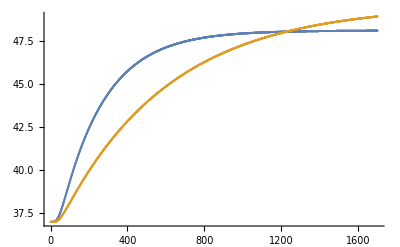

```mathematica
ListPlot[{actual,mesh[[109]]}]
```